## Calculate Lyapunov exponent

```mathematica
(* first run long ode solver for t > 1000 and obtain a points on ther orbit of attaractor. Set those points as x0,y0,and z0 (eg. solList[[1,1]][1000]=x0)*)
xmin =.1; xmax = 5;
ymin =.1; ymax = 8;
zmin = 0; zmax = 2 π;
wmin=0;wmax=5
r[x_]=√((L Sin[x])^2+h[x]);
h[x_]=d+L(1-Cos[x]);
f[x_,y_]:=y;
g[x_,y_,t_]:=3/(M L^2)(-L/2 M G Sin[x]+T Sin[Ω t]-γ ω+Abs[x]/x L μ/(4 π)m1 m2/r[x]^2 Cos[Abs[x]+ArcTan[-Abs[h[x]/(L Sin[x])]]]);
```

5

```mathematica
g[x,y,t]
```

3 (-1+Sin[t]-Sin[x]/2+(Abs[x] Cos[Abs[x]-ArcTan[Abs[(2-Cos[x]) Csc[x]]]])/(4 π x (2-Cos[x]+Sin[x]^2)))

```mathematica
3 (-1+Sin[t]-Sin[x]/2+(μ Abs[x] Cos[Abs[x]-ArcTan[Abs[(1+d-Cos[x]) Csc[x]]]])/(4 π x (1+d-Cos[θ]+Sin[x]^2)))
```

3 (-1+Sin[t]-Sin[x]/2+(Abs[x] Cos[Abs[x]-ArcTan[Abs[(2-Cos[x]) Csc[x]]]])/(4 π x (2-Cos[θ]+Sin[x]^2)))

### solving 2 close orbits

```mathematica
M=1
L=1
G=1
T=1
γ=1
ω=1
Ω=1
m1=1
m2=1
μ=1
d=1

x0=1
y0=1
```

1

1

1

«16 more identical outputs»

0

-1

0

```mathematica
(* for loop for solving ODE longer*)
solList={};
tstep =100;
steps =1;
Module[{xinit, yinit, xsol1,ysol1, tStart, tEnd, x, y,j},
xinit = x0-.001; yinit=y0-.001;
tStart =0;tEnd =tstep;
For[j = 0, j<steps, j++,
{xsol1, ysol1} =NDSolveValue[SetPrecision[{x'[t] == f[x[t],y[t]],y'[t]==g[x[t],y[t],t],x[tStart]==xinit,y[tStart]==yinit},1000],{x,y},{t,tStart,tEnd},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20]];
list = {xsol1, ysol1};
AppendTo[solList, list];
xinit = xsol1[tEnd];
yinit = ysol1[tEnd];
tStart += tstep;
tEnd += tstep;
]]
solList2={};
tstep =20;
steps =1;
Module[{xinit, yinit, xsol1, ysol1, tStart, tEnd, x, y,j},
xinit = x0; yinit=y0;tStart =0;tEnd =tstep;
For[j = 0, j<steps, j++,
{xsol1, ysol1} =NDSolveValue[SetPrecision[{x'[t] == f[x[t],y[t]],y'[t]==g[x[t],y[t],t],x[tStart]==xinit,y[tStart]==yinit},1000],{x,y},{t,tStart,tEnd},PrecisionGoal->ControlActive[4,8],WorkingPrecision->ControlActive[MachinePrecision,20]];
list = {xsol1, ysol1};
AppendTo[solList2, list];
xinit = xsol1[tEnd];
yinit = ysol1[tEnd];
tStart += tstep;
tEnd += tstep;
]]
```

### Calculating λ

```mathematica
logDelta[t_]:= Module[{deltaX, deltaY,dist,deltaZ,deltaW},
deltaX = solList[[1,1]][t]-solList2[[1,1]][t];
deltaY = solList[[1,2]][t] - solList2[[1,2]][t];

dist = Sqrt[deltaZ^2 + deltaX^2 ];
Log[dist]]
```

```mathematica
(* manipulate for linear fitting *)
Manipulate[Show[Plot[logDelta[t],{t,0,100},AxesLabel->{"ω_ct","ln|δ|"},PlotLabel->"λ∼0.09"],Plot[b + a t,{t,0,20},PlotStyle->Orange]],{a,0,2},{b,1,-10}]
```

InterpolatingFunction::dmval: Input value {20.4102} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
pts=Table[logDelta[t],{t,0,50,0.1}];
```

```mathematica
lm = LinearModelFit[pts,t,t]
```

FittedModel[-5.85224+4.13831×10^-6 t]

```mathematica
lm[20]
```

-5.85215

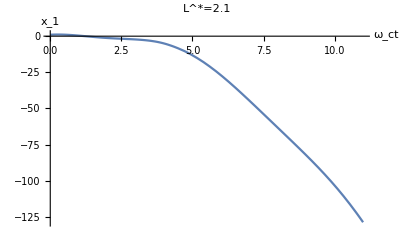

```mathematica
pieceX ={};
For[j =1, j<=Length[solList],j++,
AppendTo[pieceX, {solList[[j,1]][t],t≥100(j-1)&&t≤100 j}]]
Plot[Piecewise[pieceX],{t,0,11}, AxesLabel->{"ω_ct", "x_1"}, PlotLabel->"L^*=2.1"]
```

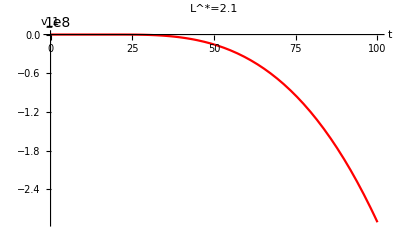

```mathematica
pieceY ={};
For[j =1, j<=Length[solList],j++,
AppendTo[pieceY, {solList[[j,2]][t],t≥100(j-1)&&t≤100 j}]]
Plot[Piecewise[pieceY],{t,0,100},PlotStyle->Red,AxesLabel->{"t", "v_1"}, PlotLabel->"L^*=2.1"]
```